# Two Flavor vacuum

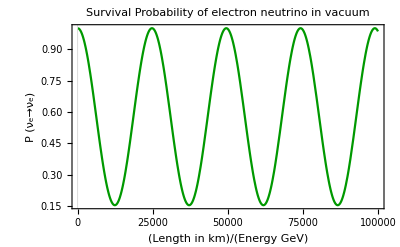

```mathematica
theta= 0.5 * ArcSin[Sqrt[0.846]];
delta= 10^-4 ;
Pv[LE_]:= 1-Sin[2*theta]^2 * Sin[1.27*delta*LE]^2;
Plot[Pv[LE],{LE,100,10^5}, PlotRange->Full, PlotLabel->"Survival Probability of electron neutrino in vacuum",PlotStyle->Directive[RGBColor[0,0.6,0]],PlotTheme-> "Scientific", FrameLabel->{{HoldForm[P (Subscript[ν, e]->Subscript[ν, e])],None},{HoldForm[Length/Energy in km/GeV],None}}]
```